# Gene drives and EUD

## Freek de Haas & Sarah P. Otto

University of British Columbia

Contact: freekdh@gmail.com

## Preliminaries

```mathematica
(*for uniformity among figures*)
LabelSize=25;
FigureSize=650;
TickSize=16;
LetterSize=20;
Pad={{70,25},{70,10}};
letpos={.05,.93};
ylabpos={-0.1,0.5};

(*set current directory to be location of this file*)
SetDirectory[NotebookDirectory[]];

(*directory to save figures in*)
imagedir="IMAGES/";

(*parent directory with simulation results*)
datadir = "SIMULATIONS/";
```

## Helper Functions

```mathematica
GameteRecombinants[gamete1_,gamete2_,pars_]:=Block[{out={},rtuples,i},
rtuples=Tuples[{gamete1,gamete2},Length[#Loci]]  &[pars];
For[i=1,i≤Length[rtuples],++i,
AppendTo[out,Table[#Gametes &[pars][[rtuples[[i]][[j]]]][[j]],{j,1,Length[#Loci &[pars]]}]] 
];
out
]
```

```mathematica
ConvertToGenotypes[Fgametes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Genotypes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[i]]=Fgametes[[Position[#Gametes  &[pars],#Genotypes  &[pars][[i]][[1]]][[1,1]]]]*Fgametes[[Position[#Gametes  &[pars],#Genotypes  &[pars][[i]][[2]]][[1,1]]]]
];
out
]
```

```mathematica
ConvertToGametes[Fgenotypes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Gametes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[1]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[2]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
];
out
]
```

```mathematica
MakeSingleDriveMatrix[WhoCutsWho_,pars_,d_]:=Block[{i,j,locations,postDriveGenotype,out},
out =IdentityMatrix[Length[#Genotypes &[pars]],SparseArray];
Assert[Length[WhoCutsWho]==2];
Assert[WhoCutsWho[[1]]≠WhoCutsWho[[2]]];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],WhoCutsWho[[1]]],
locations=Position[#Genotypes &[pars][[i]], WhoCutsWho[[2]]];
For[j=1,j≤Length[locations],++j,
postDriveGenotype=#Genotypes &[pars][[i]];
postDriveGenotype[[locations[[j]][[1]]]][[locations[[j]][[2]]]]=postDriveGenotype[[Mod[locations[[j]][[1]],2]+1]][[locations[[j]][[2]]]];
out[[i,i]]=1-d;
out[[i,Position[#Genotypes &[pars],postDriveGenotype][[1,1]]]]=d;
If[Position[#Genotypes &[pars],postDriveGenotype][[1,1]]==i,out[[i,i]]=1];
];
];
];
Transpose[out]
]

MakeDriveMatrix[WhoCutsWho_,pars_,d_]:=Block[{i,out =IdentityMatrix[Length[#Genotypes &[pars]],SparseArray]},
For[i=1,i≤Length[WhoCutsWho],++i,
out =MakeSingleDriveMatrix[WhoCutsWho[[i]],pars,d].out
];
out
]
```

```mathematica
MakeSingleMutationMatrix[WhoMutatesToWho_,pars_,μ_]:=Block[{i,j,locations,postMutationGamete,out},
out =IdentityMatrix[Length[#Gametes &[pars]],SparseArray];
For[i=1,i≤Length[#Gametes &[pars]],++i,
locations=Position[#Gametes &[pars][[i]], WhoMutatesToWho[[1]]];
For[j=1,j≤Length[locations],++j,
postMutationGamete=#Gametes &[pars][[i]];
postMutationGamete[[locations[[j]]]] = WhoMutatesToWho[[2]];
out[[i,i]]=1-μ;
out[[i,Position[#Gametes &[pars],postMutationGamete][[1,1]]]]=μ;
If[Position[#Gametes &[pars],postMutationGamete][[1,1]]==i,out[[i,i]]=1];
]
];
Transpose[out]
]

MakeMutationMatrix[WhoMutatesToWho_,pars_,μ_]:=Block[{i,out =IdentityMatrix[Length[#Gametes &[pars]],SparseArray]},
For[i=1,i≤Length[WhoMutatesToWho],++i,
out =MakeSingleMutationMatrix[WhoMutatesToWho[[i]],pars,μ].out
];
out
]
```

```mathematica
MakeFitnessMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
For[j=1,j≤Length[Payload],++j,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]],
 W[[i]]*=(1-s)^Length[Position[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]]]];
];
];
W
]
```

```mathematica
MakeDominantPayloadMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
For[j=1,j≤Length[Payload],++j,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]],
 W[[i]]=(1-s)];
];
];
W
]
```

```mathematica
Make2LocusUnderDominanceFitnessMatrix[allele_,pars_,s_]:=Block[{W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],allele[[2]]]&&!MemberQ[Flatten[Genotypes[[i]]],allele[[1]]],
 W[[i]]=(1-s)];
If[MemberQ[Flatten[Genotypes[[i]]],allele[[1]]]&&!MemberQ[Flatten[Genotypes[[i]]],allele[[2]]],
 W[[i]]=(1-s)];
];
W
]
```

```mathematica
GametesToAlleleFrequency[Gametes_,pars_]:=Block[{i,j,LociFreq,pos},
LociFreq=Table[0,{i,1,Length[#Loci &[pars]]},{j,1,2}];
For[i=1,i≤Length[#Gametes &[pars]],++i,
For[j=1,j≤Length[#Loci &[pars]],++j,
pos=Position[#Loci &[pars],#Gametes &[pars][[i]][[j]]];
LociFreq[[pos[[1,1]]]][[pos[[1,2]]]]+=Gametes[[i]];
];
];
LociFreq
]
```

## Modules

```mathematica
DiploidSelection[Fgenotypes_,pars_]:=
Block[{i,out=Table[0,{i,1,Length[Genotypes]}]},
For[i=1, i≤Length[Fgenotypes],++i,
out[[i]]=Fgenotypes[[i]]*#Fitness &[pars] [[i]];
];
out/Total[out]
]
```

```mathematica
Drive[Fgenotypes_,pars_]:=
Block[{i,j,out=Table[0,{i,1,Length[#Genotypes &[pars]]}]},
#DriveMatrix.Fgenotypes &[pars]
]
```

```mathematica
Recombination[Fgenotypes_,pars_]:=Block[
{i,j,k,n,newGamete,rec,nrec,out=Table[0,{i,1,Length[#Gametes &[pars]]}]},
n=Length[#Loci &[pars]];
rec={Array[List,ConstantArray[2,n],0,##&]};
For[i=1,i≤Length[Fgenotypes],++i,
For[j=1,j≤Length[rec],++j,
newGamete=Table[0,{i,1,n}];
For[k=1,k≤Length[#Loci &[pars]],++k,
newGamete[[k]]=#Genotypes &[pars] [[i]][[rec[[j]][[k]]+1]][[k]];
];
nrec=Length[SequenceCases[rec[[j]],{0,1}]]+
Length[SequenceCases[rec[[j]],{1,0}]];
out[[Position[#Gametes &[pars],newGamete][[1,1]]]]+=1/2 Fgenotypes[[i]](#recombination)^nrec(1-#recombination)^(Length[#Loci &[pars]]-1-nrec) &[pars];
];
];
out
]
```

```mathematica
Mutation[Fgametes_,pars_]:=Block[{i,j,out=ConstantArray[0,Length[Fgametes]],Fgenotypes,FgenotypesPrime},
Assert[Total[Fgametes]==1];
#MutationMatrix.Fgametes &[pars]
]
```

Compare to Sally

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
Wpayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0];
Wtoxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Ad"},pars,1];
W={1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s};
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"recombination"->r|>;
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm;
DriveMatrix = MakeDriveMatrix[{{"Ad","Aw"},{"Bd","Bw"}},pars,d]
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

SparseArray[<36>, {16, 16}]

```mathematica
Clear[F]
Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars][[1]]//Simplify
```

(F[1]^2-(-1+d)^2 r (-1+h s) F[2] F[3]-(-1+d) F[1] (ϵ (F[2]+F[3]-h s F[3])-(-1+d) (-1+r) (-1+h s) F[4]))/(F[1]^2+2 F[2] F[3]-2 h s F[2] F[3]+ϵ (F[2]^2-(-1+s) F[3]^2)+2 F[2] F[4]-2 h s F[2] F[4]+2 F[3] F[4]-2 s F[3] F[4]+F[4]^2-s F[4]^2+2 F[1] (ϵ (F[2]+F[3]-h s F[3])+F[4]-h s F[4]))

```mathematica
(*Sally:*)
```

```mathematica
(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))
```

(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))

## Numerical Analyses

#### Lessons learned

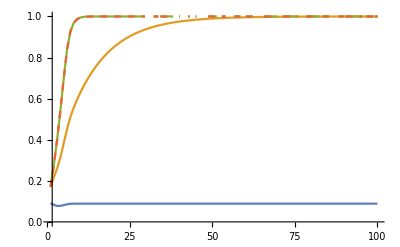
1) 
Dominance (without drive) lets underdominant construct drive to fixation. However it prevents getting rid of the initial drivers of the Daisy Chain as there is no additional "fitness cost" for these alleles. 
Conclusion: we don’t want dominance!

2) 
Recombination allows for a fitness valley between the underdominance constructs and so is necessary for EUD to work. 
Conclusion: we do want recombination (at least between the EUD constructs). Although drive seems to make recombination obsolete (?)
-Graphics-

3) 
Adding drive to EUD causes also complete fixation of AdBd, while if you don’t have drive it it won’t (see 1).
Conclusion:

Mutation-Selection balance

```mathematica
Loci={{"A0","A1"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
On[Assert]
W=ConstantArray[1,Length[Genotypes]]; 
W[[1]]=1;
W[[2]]=1-s;
W[[3]]=1-s;
W[[4]]=(1-s)^2;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W|>;
MutationMatrix=MakeMutationMatrix[{{"A0","A1"}},pars,μ];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"MutationMatrix"->MutationMatrix|>;
Off[Assert]
```

```mathematica
Clear[F]
Off[Assert]
Solve[{Mutation[ConvertToGametes[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,2}],pars],pars],pars],pars]==Table[F[i],{i,1,2}]},Table[F[i],{i,1,2}]]//FullSimplify
```

{{F[1]→0,F[2]→1},{F[1]→1-μ/s,F[2]→μ/s}}

Daisy chain 3 loci

Daisy chain implementation. Locus A drives Locus B drives Locus C.

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

Fitness=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,0.05];
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Cw"}},pars,0.999];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.01|>;
```

```mathematica
Clear[F];
F[0]={0.99,0,0,0,0,0,0,0.01};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

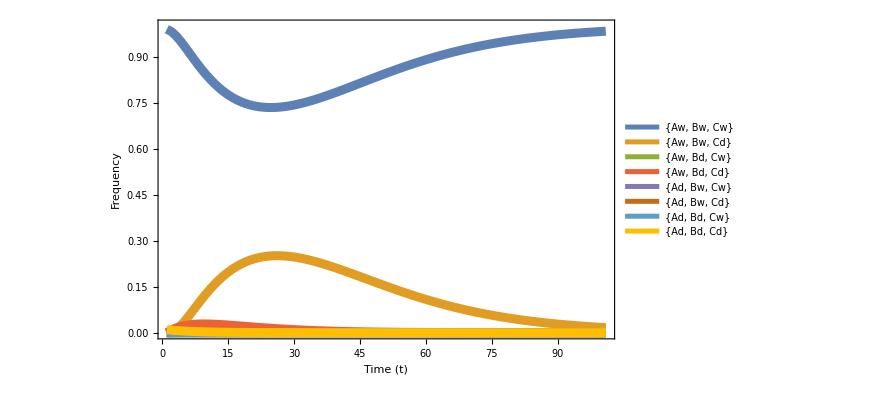

```mathematica
Show[ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}],PlotStyle->{Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style["Time (t)",LabelSize],Style["Frequency",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
]
```

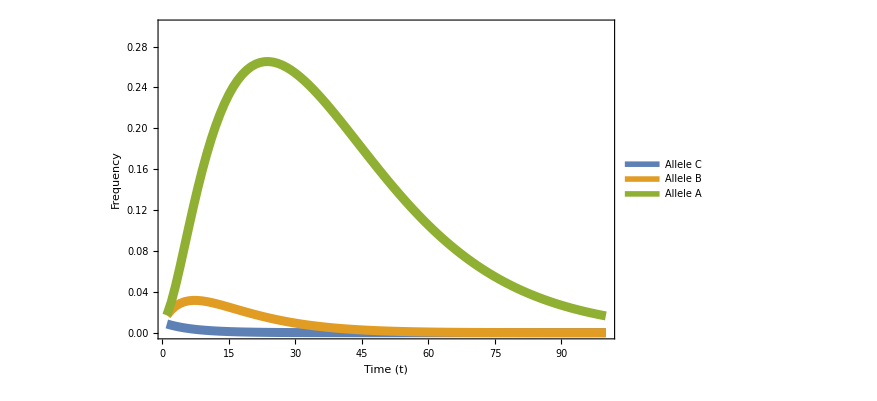

```mathematica
Legended[
Show[ListLinePlot[Transpose[Table[GametesToAlleleFrequency[F[i],pars][[;;,2]],{i,1,100}]],PlotRange->{{1,Automatic},{0,0.3}},PlotStyle->{Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style["Time (t)",LabelSize],Style["Frequency",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.1],ColorData[97,"ColorList"][[1]]],
Directive[Darker[Black],Thickness[0.1],ColorData[97,"ColorList"][[2]]],
Directive[Darker[Black],Thickness[0.1],ColorData[97,"ColorList"][[3]]]
},
{
Style["Allele C",LabelSize],
Style["Allele B",LabelSize],
Style["Allele A",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.75}
]
]
```

## Analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

Fitness=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

```mathematica
Clear[F];
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars]//Simplify;
```

```mathematica
Gametes
```

{{Aw,Bw},{Aw,Bd},{Ad,Bw},{Ad,Bd}}

```mathematica
test=eq[[2]]//Simplify
```

-(((-1+s) (F[1] (F[2]+F[4]-s F[4])-(-1+s) F[2] (F[2]+F[3]+F[4]-s F[4])))/(F[1]-(-1+s) (F[2]+F[3]+F[4]-s F[4]))^2)

```mathematica
eq[[1]]//Simplify
```

(F[1] (F[1]-(-1+s) (F[2]+F[3])))/(F[1]-(-1+s) (F[2]+F[3]+F[4]-s F[4]))^2

## Invasion Analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

Fitness=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,s];
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Cw"}},pars,d];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

```mathematica
Gametes
```

{{Aw,Bw,Cw},{Aw,Bw,Cd},{Aw,Bd,Cw},{Aw,Bd,Cd},{Ad,Bw,Cw},{Ad,Bw,Cd},{Ad,Bd,Cw},{Ad,Bd,Cd}}

```mathematica
Clear[F]
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars];
mat=Table[D[eq[[i]],F[j]],{i,2,Length[Gametes]},{j,2,Length[Gametes]}];
mat=mat/.F[1]->1/.Table[F[i]->0,{i,2,Length[Gametes]}];
```

```mathematica
mat//MatrixForm
```

((1-r)^2 (1-s)+2 (1-r) r (1-s)+r^2 (1-s) | 0 | d (1-r)^2 (1-s)^2+(1-d) (1-r) r (1-s)^2+2 d (1-r) r (1-s)^2+(1-d) r^2 (1-s)^2+d r^2 (1-s)^2 | 0 | 2 (1-r) r (1-s)^2 | 0 | (1-d) d (1-r)^2 (1-s)^3+(1-d)^2 (1-r) r (1-s)^3+(1-d) d (1-r) r (1-s)^3
0 | (1-r)^2 (1-s)+2 (1-r) r (1-s)+r^2 (1-s) | (1-d) (1-r) r (1-s)^2+(1-d) r^2 (1-s)^2 | 0 | 0 | d (1-r)^2 (1-s)^2+(1-d) (1-r) r (1-s)^2+2 d (1-r) r (1-s)^2+(1-d) r^2 (1-s)^2+d r^2 (1-s)^2 | (1-d) d (1-r)^2 (1-s)^3+(1-d)^2 r^2 (1-s)^3+(1-d) d r^2 (1-s)^3
0 | 0 | (1-d) (1-r)^2 (1-s)^2+d (1-r)^2 (1-s)^2+(1-d) (1-r) r (1-s)^2+2 d (1-r) r (1-s)^2+d r^2 (1-s)^2 | 0 | 0 | 0 | d^2 (1-r)^2 (1-s)^3+(1-d)^2 (1-r) r (1-s)^3+3 (1-d) d (1-r) r (1-s)^3+2 d^2 (1-r) r (1-s)^3+(1-d) d r^2 (1-s)^3+d^2 r^2 (1-s)^3
0 | 0 | 0 | (1-r)^2 (1-s)+2 (1-r) r (1-s)+r^2 (1-s) | 2 (1-r) r (1-s)^2 | (1-d) (1-r) r (1-s)^2+(1-d) r^2 (1-s)^2 | (1-d)^2 (1-r) r (1-s)^3
0 | 0 | 0 | 0 | (1-r)^2 (1-s)^2+r^2 (1-s)^2 | 0 | (1-d) d (1-r) r (1-s)^3+(1-d)^2 r^2 (1-s)^3+(1-d) d r^2 (1-s)^3
0 | 0 | 0 | 0 | 0 | (1-d) (1-r)^2 (1-s)^2+d (1-r)^2 (1-s)^2+(1-d) (1-r) r (1-s)^2+2 d (1-r) r (1-s)^2+d r^2 (1-s)^2 | (1-d)^2 (1-r) r (1-s)^3+2 (1-d) d (1-r) r (1-s)^3
0 | 0 | 0 | 0 | 0 | 0 | (1-d)^2 (1-r)^2 (1-s)^3+2 (1-d) d (1-r)^2 (1-s)^3+d^2 (1-r)^2 (1-s)^3+(1-d) d (1-r) r (1-s)^3+2 d^2 (1-r) r (1-s)^3+(1-d) d r^2 (1-s)^3+d^2 r^2 (1-s)^3)

```mathematica
Eigenvalues[mat]//Simplify
```

{1-s,1-s,1-s,(1+(-1+d) r) (-1+s)^2,(1+(-1+d) r) (-1+s)^2,(1-2 r+2 r^2) (-1+s)^2,(-1-(-2+d+d^2) r+(-1+d^2) r^2) (-1+s)^3}

```mathematica
Manipulate[Plot3D[(-1-(-2+d+d^2) r+(-1+d^2) r^2) (-1+s)^3,{d,0,1},{r,0,0.5},PlotRange->{Automatic,Automatic,{0,1}}],{s,0,1}]
```

```mathematica
eq=eq//Simplify;
```

$Aborted

```mathematica
neweq=eq-Table[F[i],{i,1,Length[Gametes]}]/.F[1]->1-F[2]-F[3]-F[4]-F[5]-F[6]-F[7]-F[8];
term=neweq[[2;;]]//Factor//Numerator;
```

Daisy chain 2 loci

Daisy chain implementation. Locus A drives Locus B drives Locus C.

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

Fitness=MakeFitnessMatrix[{"Ad","Bd"},pars,0.05];
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.9,0,0,0.1};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

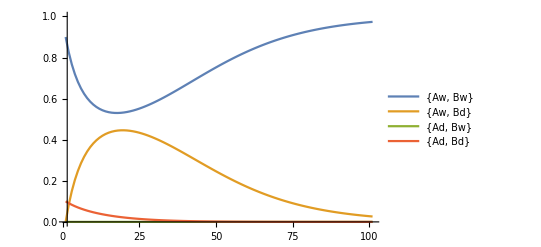

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

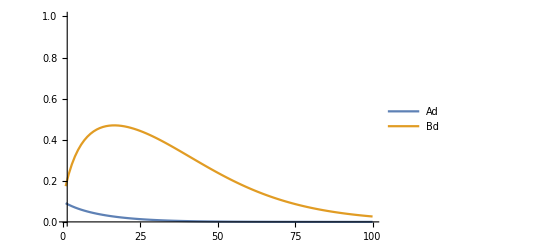

```mathematica
ListLinePlot[Transpose[Table[GametesToAlleleFrequency[F[i],pars][[;;,2]],{i,1,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Loci[[i]][[2]]],{i,1,Length[Loci]}]]
```

## Analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

Fitness=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

```mathematica
Clear[F];
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars]//Simplify;
```

```mathematica
eq[[{2,4}]]/.F[3]->0/.F[1]->1-F[2]-F[4]/.F[2]->F2[t]/.F[4]->F4[t]//FullSimplify
```

{((-1+s) (-1+s F2[t]+F4[t]) (F2[t]+F4[t]-s F4[t]))/(1-s F2[t]+(-2+s) s F4[t])^2,((-1+s)^2 F4[t])/(1-s F2[t]+(-2+s) s F4[t])}

Tried change of variables eq[[1]]/eq[[2]].

```mathematica
DSolve[{D[F2[t],t]==((-1+s) (-1+s F2[t]+F4[t]) (F2[t]+F4[t]-s F4[t]))/(1-s F2[t]+(-2+s) s F4[t])^2,D[F4[t],t]==((-1+s)^2 F4[t])/(1-s F2[t]+(-2+s) s F4[t])},{F2[t],F4[t]},t]
```

DSolve[{F2'[t]==((-1+s) (-1+s F2[t]+F4[t]) (F2[t]+F4[t]-s F4[t]))/(1-s F2[t]+(-2+s) s F4[t])^2,F4'[t]==((-1+s)^2 F4[t])/(1-s F2[t]+(-2+s) s F4[t])},{F2[t],F4[t]},t]

1 locus EUD

```mathematica
Loci={{"Aw","Ad1","Ad2"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad1","Ad2"},pars,0.2];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad1","Ad2"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness|>;
```

```mathematica
Clear[F];
F[0]={0.20,0.3,0.5}
F[t_]:=F[t]=ConvertToGametes[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

{0.2,0.3,0.5}

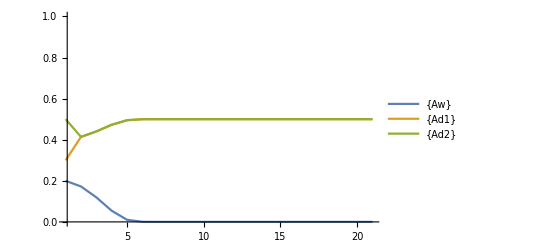

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,20}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Equilibria and Stability

```mathematica
Loci={{"Aw","Ad1","Ad2"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad1","Ad2"},pars,sp];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad1","Ad2"},pars,st];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness|>;
```

```mathematica
Clear[F]
eq=ConvertToGametes[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars]//Simplify;
```

```mathematica
sol=Solve[eq==Table[F[i],{i,1,Length[Gametes]}],Table[F[i],{i,1,Length[Gametes]}]]
```

{{F[1]→0,F[2]→1/2,F[3]→1/2},{F[1]→0,F[2]→1,F[3]→0},{F[1]→((-sp+sp^2) (-1+st))/(-sp^2-st+sp^2 st),F[2]→(-sp-st+sp st)/(-sp^2-st+sp^2 st),F[3]→0},{F[1]→((-1+sp) (-2 sp+st+sp st))/(-2 sp^2-3 st+2 sp st+sp^2 st),F[2]→(-sp-st+sp st)/(-2 sp^2-3 st+2 sp st+sp^2 st),F[3]→(-sp-st+sp st)/(-2 sp^2-3 st+2 sp st+sp^2 st)},{F[1]→1,F[2]→0,F[3]→0},{F[1]→0,F[2]→0,F[3]→1},{F[1]→((-sp+sp^2) (-1+st))/(-sp^2-st+sp^2 st),F[2]→0,F[3]→(-sp-st+sp st)/(-sp^2-st+sp^2 st)}}

```mathematica
sol[[{1,4,5}]]
```

{{F[1]→0,F[2]→1/2,F[3]→1/2},{F[1]→((-1+sp) (-2 sp+st+sp st))/(-2 sp^2-3 st+2 sp st+sp^2 st),F[2]→(-sp-st+sp st)/(-2 sp^2-3 st+2 sp st+sp^2 st),F[3]→(-sp-st+sp st)/(-2 sp^2-3 st+2 sp st+sp^2 st)},{F[1]→1,F[2]→0,F[3]→0}}

Equilibrium 1, 4 (under certain circumstances internally stable), 5,

```mathematica
sol[[4]]/.sp->1
```

{F[1]→0,F[2]→1/2,F[3]→1/2}

```mathematica
Manipulate[sol[[4]]/.sp->sp1/.st->st1,{sp1,0,1},{st1,0,1}]
```

```mathematica
Eigenvalues[mat/.sol[[4]]]//Simplify
```

{-((-3+sp) (-1+st))/(-3+2 st),(-sp^3 (-2+st)^2 (-1+st)-(-3+st) st^2+sp^2 st (6-5 st+st^2)+sp st (-6+st+st^2))/(st (-3+2 st) (sp^2 (-2+st)-3 st+2 sp st))}

```mathematica
Plot3D[(-sp^3 (-2+st)^2 (-1+st)-(-3+st) st^2+sp^2 st (6-5 st+st^2)+sp st (-6+st+st^2))/(st (-3+2 st) (sp^2 (-2+st)-3 st+2 sp st)),{sp,0,1},{st,0,1}]
```

-Graphics3D-

2 locus EUD

```mathematica
(*Lesson: you need recombination to have a fitness valley between AdAd and AwAw. Oterwise AwAw wins because higer fitness.*)
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.053];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.5,0,0,0.5};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

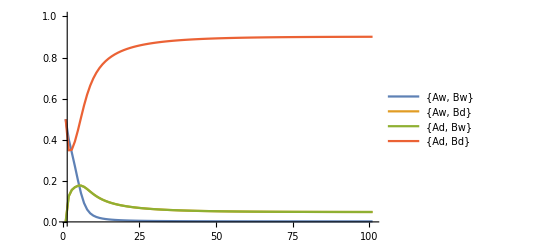

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

```mathematica
Clear[F];
F[0]={0.5466052543488716,0.12206347842681585,0.12206347842681585,0.20926778879749666};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

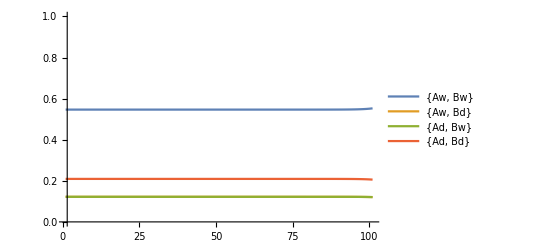

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Find unstable equilibrium analysis (using Solve)

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->r|>;

Clear[F]
eq=Recombination[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars]//Simplify;
```

```mathematica
neweq=FullSimplify[eq[[{1,4}]]/.F[2]->1/2(1-F[1]-F[4])/.F[3]->1/2(1-F[1]-F[4])];
```

```mathematica
neweq1=neweq//Simplify;
```

```mathematica
neweq1;
```

```mathematica
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}] (*takes about 10 min*)
```

{{F[1]→1,F[4]→0},{1,1},4,{F[1]→(16384 r^4 s^19-30720 r^5 s^19+29475+512 r s^26 ϵ^13 Root[1&,5]^6)/(16384 r^4 s^19-30720 r^5 s^19+11520 r^6 s^19+3229+512 r^3 s^24 ϵ^11-256 r^4 s^24 ϵ^11),F[4]→Root[-r^3 s^2-2 r^2 s^3+32+1+(1) #1^5&,5]}}
 |  |  |  |

```mathematica
Manipulate[Select[F[4]/.sol/.r->r1/.s->s1/.ϵ->ϵ1,(0<Re[#]<1&&0<=Im[#]<10^-12)&],{r1,0,0.5},{s1,0,1},{ϵ1,0,1}]
```

```mathematica
F[4]/.sol[[6]]
```

Root[-r^3 s^2-2 r^2 s^3+2 r^3 s^3+r^2 s^4-r^3 s^4-2 r^3 s ϵ-4 r^2 s^2 ϵ+6 r^3 s^2 ϵ+6 r^2 s^3 ϵ-6 r^3 s^3 ϵ-2 r^2 s^4 ϵ+2 r^3 s^4 ϵ-r^3 ϵ^2-2 r^2 s ϵ^2+4 r^3 s ϵ^2+5 r^2 s^2 ϵ^2-6 r^3 s^2 ϵ^2-4 r^2 s^3 ϵ^2+4 r^3 s^3 ϵ^2+r^2 s^4 ϵ^2-r^3 s^4 ϵ^2+(8 r s^4-6 r^2 s^4+3 r^3 s^4-4 r s^5+10 r^2 s^5-6 r^3 s^5-3 r^2 s^6+3 r^3 s^6-12 r^3 s ϵ-22 r^2 s^2 ϵ+60 r^3 s^2 ϵ+12 r s^3 ϵ+74 r^2 s^3 ϵ-108 r^3 s^3 ϵ-6 r s^4 ϵ-76 r^2 s^4 ϵ+84 r^3 s^4 ϵ-4 r s^5 ϵ+26 r^2 s^5 ϵ-24 r^3 s^5 ϵ+2 r s^6 ϵ-2 r^2 s^6 ϵ+13 r^3 ϵ^2+30 r^2 s ϵ^2-48 r^3 s ϵ^2+24 r s^2 ϵ^2-76 r^2 s^2 ϵ^2+63 r^3 s^2 ϵ^2-50 r s^3 ϵ^2+58 r^2 s^3 ϵ^2-32 r^3 s^3 ϵ^2+23 r s^4 ϵ^2-7 r^2 s^4 ϵ^2+3 r^3 s^4 ϵ^2-6 r^2 s^5 ϵ^2-r s^6 ϵ^2+r^2 s^6 ϵ^2+r^3 s^6 ϵ^2-8 r^2 ϵ^3-16 r s ϵ^3+24 r^2 s ϵ^3+24 r s^2 ϵ^3-24 r^2 s^2 ϵ^3-8 r s^3 ϵ^3+8 r^2 s^3 ϵ^3) #1+(-24 r s^6+17 r^2 s^6-3 r^3 s^6+12 r s^7-18 r^2 s^7+6 r^3 s^7+3 r^2 s^8-3 r^3 s^8+4 r^2 s^2 ϵ+12 r^3 s^2 ϵ+88 r s^3 ϵ-68 r^2 s^3 ϵ-60 r^3 s^3 ϵ-312 r s^4 ϵ+168 r^2 s^4 ϵ+100 r^3 s^4 ϵ-64 s^5 ϵ+310 r s^5 ϵ-138 r^2 s^5 ϵ-58 r^3 s^5 ϵ+48 s^6 ϵ-80 r s^6 ϵ+26 r^2 s^6 ϵ-6 r^3 s^6 ϵ-8 s^7 ϵ-6 r s^7 ϵ+6 r^2 s^7 ϵ+14 r^3 s^7 ϵ+2 r^2 s^8 ϵ-2 r^3 s^8 ϵ-16 r^3 ϵ^2-88 r^2 s ϵ^2+52 r^3 s ϵ^2-112 r s^2 ϵ^2+307 r^2 s^2 ϵ^2-53 r^3 s^2 ϵ^2-96 s^3 ϵ^2+266 r s^3 ϵ^2-366 r^2 s^3 ϵ^2+12 r^3 s^3 ϵ^2+200 s^4 ϵ^2-139 r s^4 ϵ^2+153 r^2 s^4 ϵ^2+2 r^3 s^4 ϵ^2-68 s^5 ϵ^2-46 r s^5 ϵ^2-2 r^2 s^5 ϵ^2+8 r^3 s^5 ϵ^2-12 s^6 ϵ^2+33 r s^6 ϵ^2-5 r^3 s^6 ϵ^2+4 s^7 ϵ^2+2 r s^7 ϵ^2-2 r^2 s^7 ϵ^2-2 r^2 s^8 ϵ^2+46 r^2 ϵ^3+76 r s ϵ^3-144 r^2 s ϵ^3+96 s^2 ϵ^3-164 r s^2 ϵ^3+150 r^2 s^2 ϵ^3-140 s^3 ϵ^3+84 r s^3 ϵ^3-48 r^2 s^3 ϵ^3+22 s^4 ϵ^3+28 r s^4 ϵ^3-6 r^2 s^4 ϵ^3+16 s^5 ϵ^3-24 r s^5 ϵ^3-2 s^6 ϵ^3+2 r^2 s^6 ϵ^3-12 r ϵ^4-24 s ϵ^4+32 r s ϵ^4+28 s^2 ϵ^4-24 r s^2 ϵ^4-4 s^4 ϵ^4+4 r s^4 ϵ^4) #1^2+(24 r s^8-15 r^2 s^8+r^3 s^8-12 r s^9+14 r^2 s^9-2 r^3 s^9-r^2 s^10+r^3 s^10-64 r s^4 ϵ+66 r^2 s^4 ϵ+4 r^3 s^4 ϵ+280 r s^5 ϵ-188 r^2 s^5 ϵ-8 r^3 s^5 ϵ+256 s^6 ϵ-404 r s^6 ϵ+124 r^2 s^6 ϵ-240 s^7 ϵ+168 r s^7 ϵ+46 r^2 s^7 ϵ+8 r^3 s^7 ϵ+56 s^8 ϵ-2 r s^8 ϵ-44 r^2 s^8 ϵ-4 r^3 s^8 ϵ-6 r^2 s^9 ϵ-2 r s^10 ϵ+2 r^2 s^10 ϵ+4 r^3 ϵ^2-8 r^3 s ϵ^2+256 r s^2 ϵ^2+4 r^2 s^2 ϵ^2-4 r^3 s^2 ϵ^2-776 r s^3 ϵ^2-84 r^2 s^3 ϵ^2+16 r^3 s^3 ϵ^2+320 s^4 ϵ^2+636 r s^4 ϵ^2+181 r^2 s^4 ϵ^2-4 r^3 s^4 ϵ^2-768 s^5 ϵ^2-18 r s^5 ϵ^2-84 r^2 s^5 ϵ^2-8 r^3 s^5 ϵ^2+368 s^6 ϵ^2-48 r s^6 ϵ^2-53 r^2 s^6 ϵ^2+4 r^3 s^6 ϵ^2+24 s^7 ϵ^2-34 r s^7 ϵ^2+30 r^2 s^7 ϵ^2-28 s^8 ϵ^2-11 r s^8 ϵ^2+6 r^2 s^8 ϵ^2+6 r s^9 ϵ^2+r s^10 ϵ^2-30 r^2 ϵ^3-260 r s ϵ^3+112 r^2 s ϵ^3-96 s^2 ϵ^3+724 r s^2 ϵ^3-134 r^2 s^2 ϵ^3-132 s^3 ϵ^3-532 r s^3 ϵ^3+40 r^2 s^3 ϵ^3+458 s^4 ϵ^3-28 r s^4 ϵ^3+14 r^2 s^4 ϵ^3-188 s^5 ϵ^3+76 r s^5 ϵ^3+8 r^2 s^5 ϵ^3-38 s^6 ϵ^3+20 r s^6 ϵ^3-10 r^2 s^6 ϵ^3+20 s^7 ϵ^3+4 r s^7 ϵ^3-4 r s^8 ϵ^3+72 r ϵ^4+48 s ϵ^4-192 r s ϵ^4-8 s^2 ϵ^4+144 r s^2 ϵ^4-80 s^3 ϵ^4+36 s^4 ϵ^4-24 r s^4 ϵ^4+8 s^5 ϵ^4-4 s^6 ϵ^4) #1^3+(-8 r s^10+3 r^2 s^10+4 r s^11-4 r^2 s^11-80 r s^6 ϵ+20 r^2 s^6 ϵ-320 s^7 ϵ+352 r s^7 ϵ-32 r^2 s^7 ϵ+320 s^8 ϵ-284 r s^8 ϵ-8 r^2 s^8 ϵ-48 s^9 ϵ+14 r s^9 ϵ+18 r^2 s^9 ϵ-32 s^10 ϵ+36 r s^10 ϵ+2 r^2 s^10 ϵ+8 s^11 ϵ-6 r s^11 ϵ+28 r^2 s^2 ϵ^2-272 r s^3 ϵ^2-48 r^2 s^3 ϵ^2+1016 r s^4 ϵ^2-40 r^2 s^4 ϵ^2-288 s^5 ϵ^2-1024 r s^5 ϵ^2+72 r^2 s^5 ϵ^2+752 s^6 ϵ^2+16 r s^6 ϵ^2+16 r^2 s^6 ϵ^2-320 s^7 ϵ^2+256 r s^7 ϵ^2-16 r^2 s^7 ϵ^2-144 s^8 ϵ^2+15 r s^8 ϵ^2-12 r^2 s^8 ϵ^2+84 s^9 ϵ^2-22 r s^9 ϵ^2+4 s^10 ϵ^2-5 r s^10 ϵ^2-4 s^11 ϵ^2-16 r^2 ϵ^3+200 r s ϵ^3+8 r^2 s ϵ^3-456 r s^2 ϵ^3+32 r^2 s^2 ϵ^3+272 s^3 ϵ^3+40 r s^3 ϵ^3-320 s^4 ϵ^3+352 r s^4 ϵ^3-32 r^2 s^4 ϵ^3-116 s^5 ϵ^3-20 r s^5 ϵ^3-8 r^2 s^5 ϵ^3+120 s^6 ϵ^3-124 r s^6 ϵ^3+16 r^2 s^6 ϵ^3+52 s^7 ϵ^3-4 r s^7 ϵ^3-30 s^8 ϵ^3+12 r s^8 ϵ^3-4 s^9 ϵ^3+2 s^10 ϵ^3-108 r ϵ^4-24 s ϵ^4+288 r s ϵ^4-68 s^2 ϵ^4-216 r s^2 ϵ^4+160 s^3 ϵ^4-60 s^4 ϵ^4+36 r s^4 ϵ^4-16 s^5 ϵ^4+8 s^6 ϵ^4) #1^4+(r^2 s^12+128 s^8 ϵ-96 r s^8 ϵ+6 r^2 s^8 ϵ-128 s^9 ϵ+96 r s^9 ϵ+8 r s^10 ϵ-6 r^2 s^10 ϵ+32 s^11 ϵ-24 r s^11 ϵ-8 s^12 ϵ+4 r s^12 ϵ+64 r s^4 ϵ^2+12 r^2 s^4 ϵ^2-320 r s^5 ϵ^2+64 s^6 ϵ^2+400 r s^6 ϵ^2-24 r^2 s^6 ϵ^2-192 s^7 ϵ^2-32 r s^7 ϵ^2+48 s^8 ϵ^2-132 r s^8 ϵ^2+12 r^2 s^8 ϵ^2+96 s^9 ϵ^2+16 r s^9 ϵ^2-40 s^10 ϵ^2+12 r s^10 ϵ^2-8 s^11 ϵ^2+4 s^12 ϵ^2+8 r^2 ϵ^3-128 r s^2 ϵ^3-24 r^2 s^2 ϵ^3+416 r s^3 ϵ^3-160 s^4 ϵ^3-352 r s^4 ϵ^3+24 r^2 s^4 ϵ^3+288 s^5 ϵ^3-32 r s^5 ϵ^3-80 s^6 ϵ^3+104 r s^6 ϵ^3-8 r^2 s^6 ϵ^3-72 s^7 ϵ^3+30 s^8 ϵ^3-8 r s^8 ϵ^3+4 s^9 ϵ^3-2 s^10 ϵ^3+48 r ϵ^4-128 r s ϵ^4+48 s^2 ϵ^4+96 r s^2 ϵ^4-80 s^3 ϵ^4+28 s^4 ϵ^4-16 r s^4 ϵ^4+8 s^5 ϵ^4-4 s^6 ϵ^4) #1^5&,4]

```mathematica
(*COOL! First root is unstable equilibrium, second root is stable equilibrium!
Can check with: F[1]=0.5466052543488716 ,F[2]=F[3]=0.12206347842681585,F[4]=0.20926778879749666 (s=.053, r=0.5,ϵ=1). It goes to 0.9016066889113552
*)
```

```mathematica
ArrayReshape[Fitness,{4,4}]//MatrixForm
```

(1 | (1-s) (1-ϵ) | (1-s) (1-ϵ) | (1-s)^2
(1-s) (1-ϵ) | (1-s)^2 (1-ϵ) | (1-s)^2 | (1-s)^3
(1-s) (1-ϵ) | (1-s)^2 | (1-s)^2 (1-ϵ) | (1-s)^3
(1-s)^2 | (1-s)^3 | (1-s)^3 | (1-s)^4)

2 locus EUD /w dominant payload

```mathematica
(*Lesson: you need recombination to have a fitness valley between AdAd and AwAw. Oterwise AwAw wins because higer fitness.*)
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.5|>;
```

```mathematica
Fitness
```

{1,0.,0.,0.9,0.,0.,0.9,0.9,0.,0.9,0.,0.9,0.9,0.9,0.9,0.9}

```mathematica
Clear[F];
F[0]={0.5,0,0,0.5};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

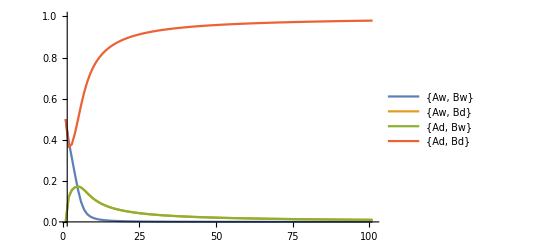

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

```mathematica
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.0005|>;
```

```mathematica
Clear[F];
F[0]={0.5,0,0,0.5};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

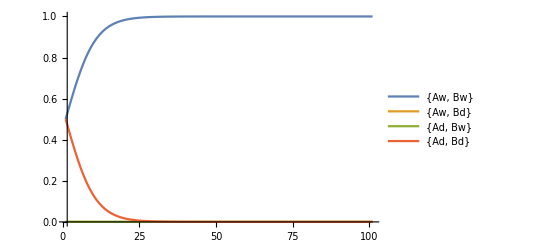

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Find unstable equilibrium analysis (using Solve)

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->r|>;

Clear[F]
eq=Recombination[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars]//Simplify;
```

```mathematica
neweq=FullSimplify[eq[[{1,4}]]/.F[2]->1/2(1-F[1]-F[4])/.F[3]->1/2(1-F[1]-F[4])];
```

```mathematica
neweq1=neweq//Simplify;
```

```mathematica
neweq1
```

{(r (-1+s) (F[1]^2+(-1+F[4])^2-2 F[1] (1+F[4]))+4 F[1] (-1+ϵ+s (-1+ϵ) (-1+F[1])+s ϵ F[4]-ϵ (F[1]+F[4])))/(2 (-2-ϵ (1+3 F[1]-F[4]) (-1+F[1]+F[4])+s (2-2 F[1]^2+ϵ (1+3 F[1]-F[4]) (-1+F[1]+F[4])))),((-1+s) (4 F[4]+r (F[1]^2+(-1+F[4])^2-2 F[1] (1+F[4]))))/(2 (-2-ϵ (1+3 F[1]-F[4]) (-1+F[1]+F[4])+s (2-2 F[1]^2+ϵ (1+3 F[1]-F[4]) (-1+F[1]+F[4]))))}

```mathematica
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}]
```

{{F[1]→0,F[4]→1},4,{F[1]→-(-2 r^2 s ϵ+2 r^2 s^2 ϵ-4 r^2 ϵ^2-11 r s ϵ^2+8 r^2 s ϵ^2+11 r s^2 ϵ^2-4 r^2 s^2 ϵ^2-26 r ϵ^3-2 s ϵ^3+52 r s ϵ^3+2 s^2 ϵ^3-26 r s^2 ϵ^3)/(4 (r^2 s^2+4 r^2 s ϵ+4 r s^2 ϵ-4 r^2 s^2 ϵ+4 r^2 ϵ^2+20 r s ϵ^2-8 r^2 s ϵ^2+1-1+4 r^2 s^2 ϵ^2+24 r ϵ^3+6 s ϵ^3-48 r s ϵ^3-6 s^2 ϵ^3+24 r s^2 ϵ^3))+1/2 √1+1/2 √1,F[4]→1/1}}
 |  |  |  |

```mathematica
sol[[3]]/.ϵ->1//Simplify
```

$Aborted

2 locus EUD and Drive

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FinessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
W=FinessPayload *FitnessToxin;
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm
DriveMatrix = MakeDriveMatrix[{{"Ad","Aw"},{"Bd","Bw"}},pars,d]
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

(1 | (1-s) (1-ϵ) | (1-s) (1-ϵ) | (1-s)^2
(1-s) (1-ϵ) | (1-s)^2 (1-ϵ) | (1-s)^2 | (1-s)^3
(1-s) (1-ϵ) | (1-s)^2 | (1-s)^2 (1-ϵ) | (1-s)^3
(1-s)^2 | (1-s)^3 | (1-s)^3 | (1-s)^4)

SparseArray[<36>, {16, 16}]

```mathematica
ArrayReshape[{1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s},{4,4}]//MatrixForm
```

(1 | ϵ | (1-h s) ϵ | 1-h s
ϵ | ϵ | 1-h s | 1-h s
(1-h s) ϵ | 1-h s | (1-s) ϵ | 1-s
1-h s | 1-h s | 1-s | 1-s)

```mathematica
Gametes
```

{{Aw,Bw},{Aw,Bd},{Ad,Bw},{Ad,Bd}}

## Invasion analysis

```mathematica
Clear[F]
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars]//Simplify;
```

```mathematica
mat=Table[D[eq[[i]],F[j]],{i,2,Length[Gametes]},{j,2,Length[Gametes]}]//Simplify;
```

```mathematica
mat=mat/.F[1]->1/.F[2]->0/.F[3]->0/.F[4]->0
```

{{(1+d) (-1+s) (-1+ϵ),0,(-1+d) (d (-1+r)-r) (-1+s)^2},{0,(1+d) (-1+s) (-1+ϵ),(-1+d) (d (-1+r)-r) (-1+s)^2},{0,0,(1-d^2 (-1+r)-r+2 d r) (-1+s)^2}}

```mathematica
Eigenvalues[mat/.F[1]->1/.F[2]->0/.F[3]->0/.F[4]->0]
```

{-(-1-d^2+r-2 d r+d^2 r) (-1+s)^2,(1+d) (-1+s) (-1+ϵ),(1+d) (-1+s) (-1+ϵ)}

```mathematica
mat[[3,3]]
```

(1-d^2 (-1+r)-r+2 d r) (-1+s)^2

```mathematica
critr=Solve[mat[[3,3]]==1,r]
```

{{r→(d^2-2 s-2 d^2 s+s^2+d^2 s^2)/((-1+d)^2 (-1+s)^2)}}

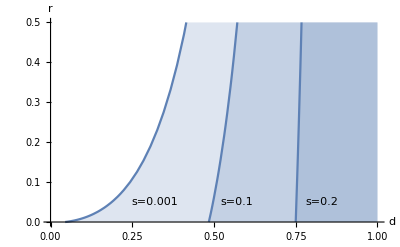

```mathematica
Show[
Plot[r/.critr/.s ->{0.001,0.1,0.2},{d,0,1},PlotRange->{Automatic,{0,0.5}},Filling->Bottom,AxesLabel->{"d","r"}],
Graphics[Text["s=0.001",{0.32,0.05}]],
Graphics[Text["s=0.1",{0.57,0.05}]],
Graphics[Text["s=0.2",{0.83,0.05}]]
]
```

## Find unstable equilibrium analysis

```mathematica
Clear[s]
```

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
(*W={1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s};*)
FinessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
W=FinessPayload *FitnessToxin;
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm;
DriveMatrix = MakeDriveMatrix[{{"Ad","Aw"},{"Bd","Bw"}},pars,d]
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"DriveMatrix"->DriveMatrix,"recombination"->r|>;

Clear[F]
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars]//Simplify;
```

SparseArray[<36>, {16, 16}]

```mathematica
neweq=FullSimplify[eq[[{1,4}]]/.F[2]->1/2(1-F[1]-F[4])/.F[3]->1/2(1-F[1]-F[4])];
```

```mathematica
neweq-{F[1],F[4]}//Factor//Numerator;
```

```mathematica
neweq1=neweq/.ϵ->1/.d->1//Simplify;
```

```mathematica
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}]
```

{{F[1]→1,F[4]→0},{F[1]→0,F[4]→1},{F[1]→(-1+s)^4/((-2+s)^2 s^2),F[4]→(-1+4 s-2 s^2)/((-2+s)^2 s^2)}}

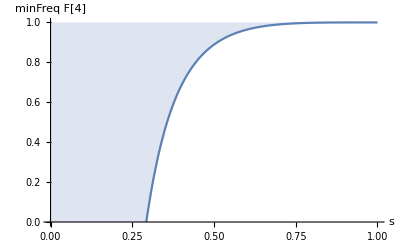

```mathematica
Plot[(-1+4 s-2 s^2)/((-2+s)^2 s^2),{s,0,1},PlotRange->{Automatic,{0,1}},Filling->Top,AxesLabel->{"s","minFreq F[4]"}]
```

```mathematica
(*does not depend on r anymore*)
```

### Try 2

```mathematica
neweq2=neweq/.ϵ->1/.r->1/2
```

{(F[1]^2+1/2 (-1+d)^2 (-1+s)^2 F[1] F[4]+1/8 (-1+d)^2 (-1+s)^2 (-1+F[1]+F[4])^2)/(F[1]^2+2 (-1+s) F[1] (-F[4]+s F[4])+1/2 (-1+s)^2 (-(-1+F[1]+F[4])^2+2 (-1+F[1]+s F[4])^2)),((-1+s)^2 ((1/2 (-1+d)^2+2 d) (-1+F[1])^2-2 (1/2 (-1+d)^2 (1+F[1])+2 (-1+s+d s-(s+d (d+s)) F[1])) F[4]+(1/2+d^2/2-2 d (3/2-2 s)+4 (-1+s) s) F[4]^2))/(4-4 s (-1+F[1])^2+2 s^2 (-1+F[1])^2+2 (-1+F[1]) (1+3 F[1])+4 (-1+s) (-1+s (3-F[1])+2 s^2 (-1+F[1])-F[1]) F[4]+2 (-1+s)^2 (-1+2 s^2) F[4]^2)}

```mathematica
sol=Solve[neweq2=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
Manipulate[F[4]/.sol/.d->d1/.s->s1,{d1,0,1},{s1,0,1}]
```

```mathematica
Manipulate[Plot[-1-2 d+3 d^2+12 d^3+13 d^4+6 d^5+d^6-2 s-12 d s-30 d^2 s-40 d^3 s-30 d^4 s-12 d^5 s-2 d^6 s+s^2+6 d s^2+15 d^2 s^2+20 d^3 s^2+15 d^4 s^2+6 d^5 s^2+d^6 s^2+(-3+12 d+59 d^2+70 d^3+19 d^4-16 d^5-11 d^6-2 d^7-16 s-134 d s-332 d^2 s-330 d^3 s-88 d^4 s+70 d^5 s+52 d^6 s+10 d^7 s+71 s^2+342 d s^2+637 d^2 s^2+528 d^3 s^2+97 d^4 s^2-146 d^5 s^2-101 d^6 s^2-20 d^7 s^2-44 s^3-212 d s^3-388 d^2 s^3-292 d^3 s^3+12 d^4 s^3+164 d^5 s^3+100 d^6 s^3+20 d^7 s^3+12 s^4+58 d s^4+102 d^2 s^4+58 d^3 s^4-48 d^4 s^4-90 d^5 s^4-50 d^6 s^4-10 d^7 s^4-2 s^5-10 d s^5-18 d^2 s^5-10 d^3 s^5+10 d^4 s^5+18 d^5 s^5+10 d^6 s^5+2 d^7 s^5) x+(28+164 d+193 d^2-106 d^3-261 d^4-56 d^5+71 d^6+30 d^7+d^8-172 s-978 d s-1176 d^2 s+450 d^3 s+1324 d^4 s+306 d^5 s-352 d^6 s-162 d^7 s-8 d^8 s+673 s^2+2838 d s^2+3159 d^2 s^2-712 d^3 s^2-2885 d^4 s^2-834 d^5 s^2+689 d^6 s^2+372 d^7 s^2+28 d^8 s^2-1148 s^3-4164 d s^3-4356 d^2 s^3+708 d^3 s^3+3684 d^4 s^3+1380 d^5 s^3-684 d^6 s^3-484 d^7 s^3-56 d^8 s^3+800 s^4+2858 d s^4+2946 d^2 s^4-682 d^3 s^4-2990 d^4 s^4-1370 d^5 s^4+390 d^6 s^4+410 d^7 s^4+70 d^8 s^4-298 s^5-1078 d s^5-1098 d^2 s^5+434 d^3 s^5+1498 d^4 s^5+766 d^5 s^5-174 d^6 s^5-250 d^7 s^5-56 d^8 s^5+64 s^6+244 d s^6+256 d^2 s^6-136 d^3 s^6-436 d^4 s^6-220 d^5 s^6+88 d^6 s^6+112 d^7 s^6+28 d^8 s^6-8 s^7-32 d s^7-32 d^2 s^7+32 d^3 s^7+80 d^4 s^7+32 d^5 s^7-32 d^6 s^7-32 d^7 s^7-8 d^8 s^7+s^8+4 d s^8+4 d^2 s^8-4 d^3 s^8-10 d^4 s^8-4 d^5 s^8+4 d^6 s^8+4 d^7 s^8+d^8 s^8) x^2+(232+104 d-492 d^2-352 d^3+272 d^4+248 d^5-76 d^6-64 d^7-1208 s-1184 d s+2368 d^2 s+2864 d^3 s-1048 d^4 s-1664 d^5 s+272 d^6 s+368 d^7 s+3400 s^2+5192 d s^2-4996 d^2 s^2-9600 d^3 s^2+1376 d^4 s^2+4952 d^5 s^2-164 d^6 s^2-928 d^7 s^2-7000 s^3-12456 d s^3+5952 d^2 s^3+17808 d^3 s^3-24 d^4 s^3-8392 d^5 s^3-592 d^6 s^3+1376 d^7 s^3+9114 s^4+16808 d s^4-4662 d^2 s^4-20752 d^3 s^4-2146 d^4 s^4+8920 d^5 s^4+1310 d^6 s^4-1360 d^7 s^4-6776 s^5-12536 d s^5+3272 d^2 s^5+15936 d^3 s^5+2744 d^4 s^5-6392 d^5 s^5-1288 d^6 s^5+944 d^7 s^5+3054 s^6+5520 d s^6-2042 d^2 s^6-8080 d^3 s^6-1510 d^4 s^6+3328 d^5 s^6+818 d^6 s^6-448 d^7 s^6-856 s^7-1496 d s^7+856 d^2 s^7+2640 d^3 s^7+376 d^4 s^7-1272 d^5 s^7-376 d^6 s^7+128 d^7 s^7+143 s^8+246 d s^8-195 d^2 s^8-524 d^3 s^8-55 d^4 s^8+294 d^5 s^8+107 d^6 s^8-16 d^7 s^8-10 s^9-20 d s^9+10 d^2 s^9+40 d^3 s^9+10 d^4 s^9-20 d^5 s^9-10 d^6 s^9-s^10-2 d s^10+d^2 s^10+4 d^3 s^10+d^4 s^10-2 d^5 s^10-d^6 s^10) x^3+(-464+112 d+680 d^2-64 d^3-400 d^4+112 d^5+56 d^6+1776 s+144 d s-3024 d^2 s-96 d^3 s+1616 d^4 s-304 d^5 s-240 d^6 s-3112 s^2-1328 d s^2+4904 d^2 s^2+768 d^3 s^2-2280 d^4 s^2+144 d^5 s^2+328 d^6 s^2+2432 s^3+1568 d s^3-1824 d^2 s^3-288 d^3 s^3+64 d^4 s^3+64 d^5 s^3+32 d^6 s^3+2432 s^4+1888 d s^4-5712 d^2 s^4-2800 d^3 s^4+3968 d^4 s^4+624 d^5 s^4-656 d^6 s^4-7408 s^5-6184 d s^5+10400 d^2 s^5+6192 d^3 s^5-5616 d^4 s^5-1736 d^5 s^5+1024 d^6 s^5+6392 s^6+5680 d s^6-8152 d^2 s^6-6336 d^3 s^6+3848 d^4 s^6+2064 d^5 s^6-936 d^6 s^6-2384 s^7-2520 d s^7+3120 d^2 s^7+3760 d^3 s^7-1488 d^4 s^7-1560 d^5 s^7+560 d^6 s^7+100 s^8+668 d s^8-130 d^2 s^8-1472 d^3 s^8+216 d^4 s^8+820 d^5 s^8-202 d^6 s^8+260 s^9-168 d s^9-452 d^2 s^9+432 d^3 s^9+156 d^4 s^9-264 d^5 s^9+36 d^6 s^9-106 s^10+36 d s^10+210 d^2 s^10-72 d^3 s^10-102 d^4 s^10+36 d^5 s^10-2 d^6 s^10+16 s^11-32 d^2 s^11+16 d^4 s^11) x^4+(208-256 d-96 d^2+256 d^3-112 d^4-512 s+576 d s+256 d^2 s-576 d^3 s+256 d^4 s+208 s^2-192 d s^2+352 d^2 s^2-320 d^3 s^2+80 d^4 s^2+1024 s^3-768 d s^3-1792 d^2 s^3+2048 d^3 s^3-640 d^4 s^3-2200 s^4+1312 d s^4+1808 d^2 s^4-1952 d^3 s^4+552 d^4 s^4+960 s^5-800 d s^5+896 d^2 s^5-544 d^3 s^5+1792 s^6-192 d s^6-3328 d^2 s^6+2432 d^3 s^6-320 d^4 s^6-2240 s^7+800 d s^7+2432 d^2 s^7-1760 d^3 s^7+256 d^4 s^7+740 s^8-640 d s^8-88 d^2 s^8+96 d^3 s^8+20 d^4 s^8+224 s^9+128 d s^9-864 d^2 s^9+704 d^3 s^9-192 d^4 s^9-268 s^10+112 d s^10+584 d^2 s^10-560 d^3 s^10+132 d^4 s^10+96 s^11-64 d s^11-192 d^2 s^11+192 d^3 s^11-32 d^4 s^11-14 s^12+8 d s^12+28 d^2 s^12-24 d^3 s^12+2 d^4 s^12) x^5,{x,0,1}],{s,0,1},{d,0,1}]
```

## Numerical

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
(*W={1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s};*)
FinessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.3];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
W=FinessPayload *FitnessToxin;
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm;
DriveMatrix = MakeDriveMatrix[{{"Ad","Aw"},{"Bd","Bw"}},pars,0.95]
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"DriveMatrix"->DriveMatrix,"recombination"->0.5|>;
```

SparseArray[<36>, {16, 16}]

```mathematica
Clear[F];
F[0]={0.95,0,0,0.05};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

```mathematica
F[1]
```

{0.841775,0.00369287,0.00369287,0.15084}

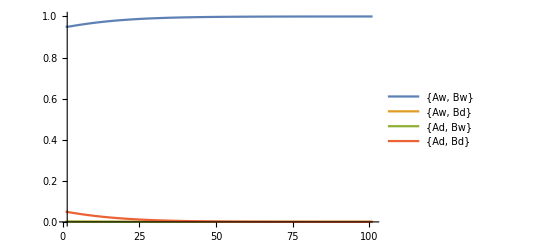

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

3 locus Daisy Chain and EUD

Once Bd is gone drive is weak/absent. But it appears that a polymorphism is stable with underdominance and recombination, need to CHECK! analytically. Recall that the underdominance is only acting on matings between CdDw and CwDd

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Cd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Ad","Cw"}},pars,0.99];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.8,0,0,0,0,0,0,0.2};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

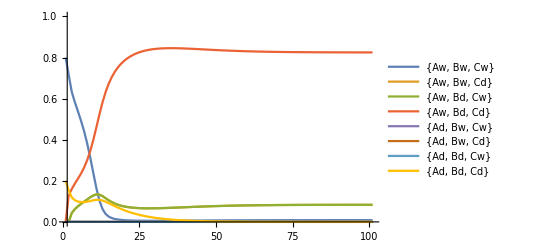

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

```mathematica
F[100]
```

{1.,8.98395×10^-14,8.98395×10^-14,1.59471×10^-13,1.33326×10^-9,3.51676×10^-16,3.51676×10^-16,6.99835×10^-14}

```mathematica
(*It approaches the same equilibrium as the 2 locus EUD *)
```

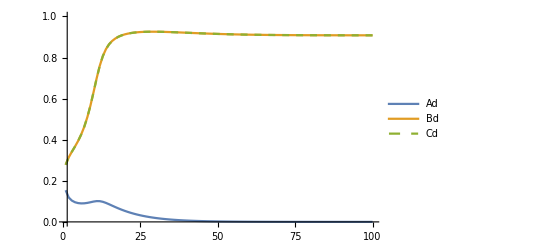

```mathematica
ListLinePlot[Transpose[Table[GametesToAlleleFrequency[F[i],pars][[;;,2]],{i,1,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Loci[[i]][[2]]],{i,1,Length[Loci]}],PlotStyle->{0,0,Dashed}]
```

## Invasion analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Cd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Ad","Cw"}},pars,d];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

```mathematica
Clear[F]
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars]//Simplify;
```

```mathematica
mat=Table[D[eq[[i]],F[j]],{i,2,Length[Gametes]},{j,2,Length[Gametes]}];
```

```mathematica
mat=mat/.F[1]->1/.Table[F[i]->0,{i,2,Length[Gametes]}]//Factor
```

{{(-1+s) (-1+ϵ),0,r (-1+s)^2,0,-(d+2 r-2 d r-2 r^2+2 d r^2) (-1+s)^2 (-1+ϵ),0,(-1+d) (-1+r) (-d-r+d r) (-1+s)^3},{0,(-1+s) (-1+ϵ),r (-1+s)^2,0,0,(-d-r+d r) (-1+s)^2 (-1+ϵ),(-1+d) (d-2 d r+r^2+d r^2) (-1+s)^3},{0,0,-(-1+r) (-1+s)^2,0,0,0,-(d^2+r+d r-2 d^2 r-r^2+d^2 r^2) (-1+s)^3},{0,0,0,1-s,-2 (-1+d) (-1+r) r (-1+s)^2 (-1+ϵ),(-1+d) r (-1+s)^2 (-1+ϵ),(-1+d)^2 (-1+r) r (-1+s)^3},{0,0,0,0,(-1+2 r-2 d r-2 r^2+2 d r^2) (-1+s)^2 (-1+ϵ),0,-(-1+d) r (-d-r+d r) (-1+s)^3},{0,0,0,0,0,-(1-r+d r) (-1+s)^2 (-1+ϵ),-(-1+d) (1+d) (-1+r) r (-1+s)^3},{0,0,0,0,0,0,(-1+2 r-d r-d^2 r-r^2+d^2 r^2) (-1+s)^3}}

```mathematica
MatrixForm[mat]
```

((-1+s) (-1+ϵ) | 0 | r (-1+s)^2 | 0 | -(d+2 r-2 d r-2 r^2+2 d r^2) (-1+s)^2 (-1+ϵ) | 0 | (-1+d) (-1+r) (-d-r+d r) (-1+s)^3
0 | (-1+s) (-1+ϵ) | r (-1+s)^2 | 0 | 0 | (-d-r+d r) (-1+s)^2 (-1+ϵ) | (-1+d) (d-2 d r+r^2+d r^2) (-1+s)^3
0 | 0 | -(-1+r) (-1+s)^2 | 0 | 0 | 0 | -(d^2+r+d r-2 d^2 r-r^2+d^2 r^2) (-1+s)^3
0 | 0 | 0 | 1-s | -2 (-1+d) (-1+r) r (-1+s)^2 (-1+ϵ) | (-1+d) r (-1+s)^2 (-1+ϵ) | (-1+d)^2 (-1+r) r (-1+s)^3
0 | 0 | 0 | 0 | (-1+2 r-2 d r-2 r^2+2 d r^2) (-1+s)^2 (-1+ϵ) | 0 | -(-1+d) r (-d-r+d r) (-1+s)^3
0 | 0 | 0 | 0 | 0 | -(1-r+d r) (-1+s)^2 (-1+ϵ) | -(-1+d) (1+d) (-1+r) r (-1+s)^3
0 | 0 | 0 | 0 | 0 | 0 | (-1+2 r-d r-d^2 r-r^2+d^2 r^2) (-1+s)^3)

```mathematica
Eigenvalues[mat/.F[1]->1/.F[2]->0/.F[3]->0/.F[4]->0]/.ϵ->1
```

{1-s,-(-1+r) (-1+s)^2,(-1+2 r-d r-d^2 r-r^2+d^2 r^2) (-1+s)^3,0,0,0,0}

```mathematica
(*This equilibrium is always stable!*)
```

## Find unstable equilibrium analysis - wrong!

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Cd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Ad","Cw"}},pars,d];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->r|>;

Clear[F]
eq=Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars]//Simplify;
```

```mathematica
(*We can make use of the fact that F[2][[t]]=F[3][[t]] when F[2][[0]]=F[3][[0]]. Same goes for F[6] and F[7].
So we are only interested in 1,2,4,5,6,8. We can again get rid of one by assuming they add up to 1.*)
```

```mathematica
neweq=eq[[{1,2,5,6,8}]]/.F[4]->1-F[1]-F[2]-F[3]-F[5]-F[6]-F[7]-F[8]/.F[3]->F[2]/.F[7]->F[6];
```

```mathematica
neweq2=neweq-{F[1],F[2],F[5],F[6],F[8]};
```

```mathematica
testeq=neweq2/.s->0.4/.r->0.5/.ϵ->1/.d->1;
```

```mathematica
NSolve[testeq==Table[0,{i,1,5}],{F[1],F[2],F[5],F[6],F[8]}]
```

{{F[8]→0,F[2]→0,F[6]→0,F[5]→0,F[1]→1.},{F[8]→0.0718357,F[2]→0.259329,F[6]→0,F[5]→0.939775,F[1]→-0.475679},{F[8]→0.0718357,F[2]→0.259329,F[6]→0,F[5]→0.939775,F[1]→-0.475679},{F[8]→0.0718357,F[2]→0.259329,F[6]→0,F[5]→0.939775,F[1]→-0.475679},{F[8]→0,F[2]→0.569632+0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977-0.215779 ⅈ},{F[8]→0,F[2]→0.569632-0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977+0.215779 ⅈ},{F[8]→0,F[2]→0.569632+0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977-0.215779 ⅈ},{F[8]→0,F[2]→0.569632-0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977+0.215779 ⅈ},{F[8]→0,F[2]→0.569632-0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977+0.215779 ⅈ},{F[8]→0,F[2]→0.569632-0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977+0.215779 ⅈ},{F[8]→0,F[2]→0.569632-0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977+0.215779 ⅈ},{F[8]→0,F[2]→0.569632-0.201482 ⅈ,F[6]→0,F[5]→0,F[1]→0.120977+0.215779 ⅈ},{F[8]→-0.404669-0.267786 ⅈ,F[2]→0.456563+0.241021 ⅈ,F[6]→0,F[5]→0,F[1]→0.152217-0.181078 ⅈ},{F[8]→-0.404669-0.267786 ⅈ,F[2]→0.456563+0.241021 ⅈ,F[6]→0,F[5]→0,F[1]→0.152217-0.181078 ⅈ},{F[8]→-0.404669-0.267786 ⅈ,F[2]→0.456563+0.241021 ⅈ,F[6]→0,F[5]→0,F[1]→0.152217-0.181078 ⅈ},{F[8]→-0.404669+0.267786 ⅈ,F[2]→0.456563-0.241021 ⅈ,F[6]→0,F[5]→0,F[1]→0.152217+0.181078 ⅈ},{F[8]→1.54688,F[2]→-0.157646,F[6]→0,F[5]→-0.377368,F[1]→0.178461},{F[8]→0,F[2]→0.215399-0.0110796 ⅈ,F[6]→0,F[5]→0,F[1]→0.04936-0.0978537 ⅈ},{F[8]→1.21027-0.467298 ⅈ,F[2]→-0.0375669+0.0527493 ⅈ,F[6]→0,F[5]→0,F[1]→0.0862403-0.0557071 ⅈ},{F[8]→1.21027+0.467298 ⅈ,F[2]→-0.0375669-0.0527493 ⅈ,F[6]→0,F[5]→0,F[1]→0.0862403+0.0557071 ⅈ},{F[8]→1.21027-0.467298 ⅈ,F[2]→-0.0375669+0.0527493 ⅈ,F[6]→0,F[5]→0,F[1]→0.0862403-0.0557071 ⅈ},{F[8]→1.21027-0.467298 ⅈ,F[2]→-0.0375669+0.0527493 ⅈ,F[6]→0,F[5]→0,F[1]→0.0862403-0.0557071 ⅈ},{F[8]→1.10967,F[2]→-0.0123732,F[6]→0,F[5]→0.117581,F[1]→0.0336987},{F[8]→1.,F[2]→0,F[6]→0,F[5]→0,F[1]→0},{F[8]→0.83692+0.0403864 ⅈ,F[2]→-0.0305733+0.0188331 ⅈ,F[6]→0,F[5]→0,F[1]→-0.00537112-0.00825195 ⅈ},{F[8]→0.83692-0.0403864 ⅈ,F[2]→-0.0305733-0.0188331 ⅈ,F[6]→0,F[5]→0,F[1]→-0.00537112+0.00825195 ⅈ},{F[8]→0.83692-0.0403864 ⅈ,F[2]→-0.0305733-0.0188331 ⅈ,F[6]→0,F[5]→0,F[1]→-0.00537112+0.00825195 ⅈ},{F[8]→0.83692+0.0403864 ⅈ,F[2]→-0.0305733+0.0188331 ⅈ,F[6]→0,F[5]→0,F[1]→-0.00537112-0.00825195 ⅈ},{F[8]→0.83692+0.0403864 ⅈ,F[2]→-0.0305733+0.0188331 ⅈ,F[6]→0,F[5]→0,F[1]→-0.00537112-0.00825195 ⅈ},{F[8]→0.83692-0.0403864 ⅈ,F[2]→-0.0305733-0.0188331 ⅈ,F[6]→0,F[5]→0,F[1]→-0.00537112+0.00825195 ⅈ},{F[8]→0,F[2]→0.039121,F[6]→0,F[5]→0,F[1]→-0.0171423},{F[8]→0,F[2]→0.039121,F[6]→0,F[5]→0,F[1]→-0.0171423}}

```mathematica
sol=Select[{F[1],F[2],F[5],F[6],F[8]}/.NSolve[testeq==Table[0,{i,1,5}],{F[1],F[2],F[5],F[6],F[8]}],(0<Re[#[[1]]]<1&&0<Re[#[[2]]]<1&&0<Re[#[[3]]]<1&&0<Re[#[[4]]]<1&&0<Re[#[[5]]]<1)&](*(0<Re[#[[1]]]<1&&0<Re[#[[2]]]<1&&0<Re[#[[3]]]<1&&0<Re[#[[4]]]<1&&0<Re[#[[5]]]<1&&0<Re[#[[6]]]<1&&0<Re[#[[7]]]<1&&0<Re[#[[8]]]<1)&]*)
```

{}

3 locus Daisy Chain and EUD /w dominant payload

Once Bd is gone drive is weak/absent. But it appears that a polymorphism is stable with underdominance and recombination, need to CHECK! analytically. Recall that the underdominance is only acting on matings between CdDw and CwDd

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd","Cd"},pars,0.2];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Cd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Ad","Cw"}},pars,0.95];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.000000005|>;
```

```mathematica
ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm
```

(1 | 0. | 0. | 0.8 | 0.8 | 0. | 0. | 0.8
0. | 0. | 0.8 | 0.8 | 0. | 0. | 0.8 | 0.8
0. | 0.8 | 0. | 0.8 | 0. | 0.8 | 0. | 0.8
0.8 | 0.8 | 0.8 | 0.8 | 0.8 | 0.8 | 0.8 | 0.8
0.8 | 0. | 0. | 0.8 | 0.8 | 0. | 0. | 0.8
0. | 0. | 0.8 | 0.8 | 0. | 0. | 0.8 | 0.8
0. | 0.8 | 0. | 0.8 | 0. | 0.8 | 0. | 0.8
0.8 | 0.8 | 0.8 | 0.8 | 0.8 | 0.8 | 0.8 | 0.8)

```mathematica
Gametes
```

{{Aw,Bw,Cw},{Aw,Bw,Cd},{Aw,Bd,Cw},{Aw,Bd,Cd},{Ad,Bw,Cw},{Ad,Bw,Cd},{Ad,Bd,Cw},{Ad,Bd,Cd}}

```mathematica
Clear[F];
F[0]={0.8,0,0,0,0,0,0,0.2};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

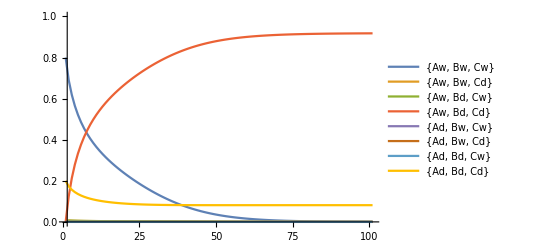

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

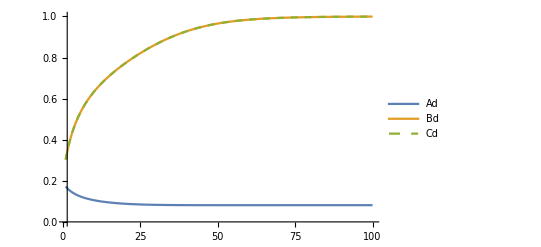

```mathematica
ListLinePlot[Transpose[Table[GametesToAlleleFrequency[F[i],pars][[;;,2]],{i,1,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Loci[[i]][[2]]],{i,1,Length[Loci]}],PlotStyle->{0,0,Dashed}]
```

```mathematica
(*Ad is at some point only on a background with Bd and Cd. Due to dominance the "cost" for carrying Ad is not felt.*)
```

4 locus Daisy chain and EUD

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd","Dd"},pars,0.045];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,0.99];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,0.95];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.95,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.05};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

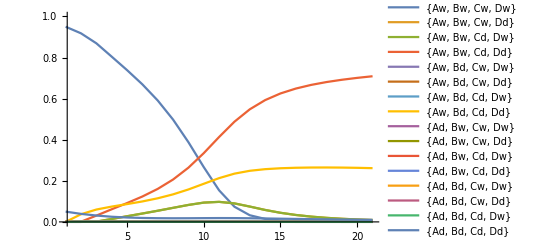

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,20}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

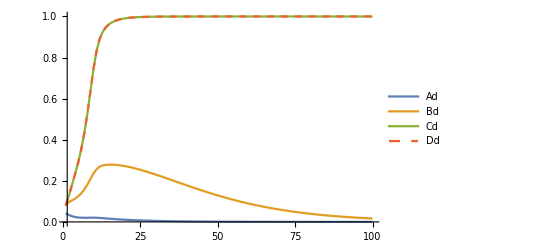

```mathematica
ListLinePlot[Transpose[Table[GametesToAlleleFrequency[F[i],pars][[;;,2]],{i,1,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Loci[[i]][[2]]],{i,1,Length[Loci]}],PlotStyle->{0,0,0,Dashed}]
```

4 locus Daisy chain and EUD /w dominant payload

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd","Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,0.95];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

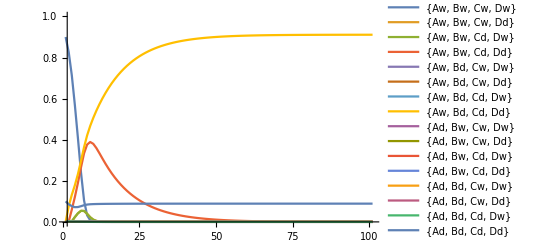

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

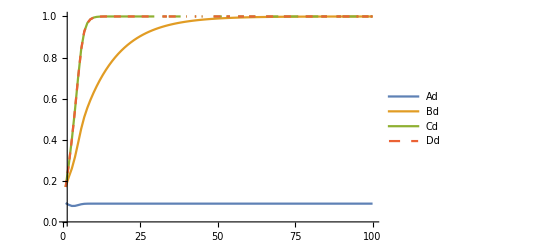

```mathematica
ListLinePlot[Transpose[Table[GametesToAlleleFrequency[F[i],pars][[;;,2]],{i,1,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Loci[[i]][[2]]],{i,1,Length[Loci]}],PlotStyle->{0,0,0,Dashed}]
```

Migration (1 way)

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Cd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Ad","Cw"}},pars,0.95];

pars1=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->0.5|>;
```

```mathematica
Clear[F1,F2,F3,F4];
F1[0]={0.8,0,0,0,0,0,0,0.2};
F2[0]={1.0,0,0,0,0,0,0,0};
F3[0]={1.0,0,0,0,0,0,0,0};
F4[0]={1.0,0,0,0,0,0,0,0};

F1[t_]:=F1[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F1[t-1],pars1],pars1],pars1],pars1]
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1]-0.01(F2[t-1]-F1[t-1]),pars1],pars1],pars1],pars1]
F3[t_]:=F3[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F3[t-1]-0.01(F3[t-1]-F2[t-1]),pars1],pars1],pars1],pars1]
F4[t_]:=F4[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F4[t-1]-0.01(F4[t-1]-F3[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P1=ListLinePlot[Transpose[Table[F1[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 1",AxesLabel->{"Gen","Freq"}];
P2=ListLinePlot[Transpose[Table[F2[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 2",AxesLabel->{"Gen","Freq"}];
P3=ListLinePlot[Transpose[Table[F3[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 3",AxesLabel->{"Gen","Freq"}];
Load1=ListLinePlot[Table[1-ConvertToGenotypes[F1[i],pars].Fitness,{i,1,100}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
Load2=ListLinePlot[Table[1-ConvertToGenotypes[F2[i],pars].Fitness,{i,1,100}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
Load3=ListLinePlot[Table[1-ConvertToGenotypes[F3[i],pars].Fitness,{i,1,100}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
```

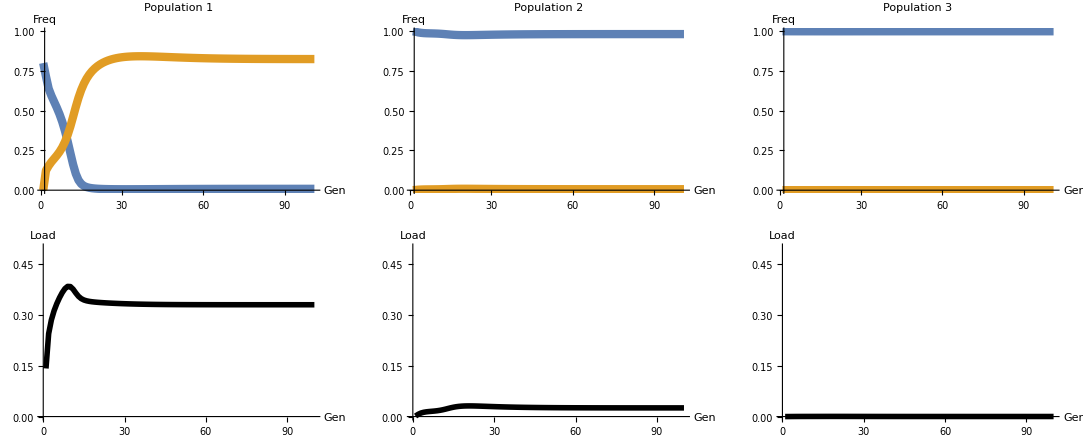

```mathematica
GraphicsGrid[{{P1,P2,P3},{Load1,Load2,Load3}}]
```

Migration (2 way)

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd"},pars,0.05];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Cd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Ad","Cw"}},pars,1];

pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix|>;
```

```mathematica
Clear[F1,F2,F3,F4];
F1[0]={0.7,0,0,0,0,0,0,0.3};
F2[0]={1.0,0,0,0,0,0,0,0};
F3[0]={1.0,0,0,0,0,0,0,0};
F4[0]={1.0,0,0,0,0,0,0,0};

m=0.03;
F1[t_]:=F1[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F1[t-1]-m(F1[t-1]-F2[t-1]),pars1],pars1],pars1],pars1]
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1]-m(F2[t-1]-(F1[t-1]+F3[t-1])/2),pars1],pars1],pars1],pars1]
F3[t_]:=F3[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F3[t-1]-m(F3[t-1]-(F2[t-1]+F4[t-1])/2),pars1],pars1],pars1],pars1]
F4[t_]:=F4[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F4[t-1]-m(F4[t-1]-F3[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
tmax=100;
P1=ListLinePlot[Transpose[Table[F1[t],{t,0,tmax}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 1",AxesLabel->{"Gen","Freq"}];
P2=ListLinePlot[Transpose[Table[F2[t],{t,0,tmax}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 2",AxesLabel->{"Gen","Freq"}];
P3=ListLinePlot[Transpose[Table[F3[t],{t,0,tmax}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 3",AxesLabel->{"Gen","Freq"}];
P4=ListLinePlot[Transpose[Table[F4[t],{t,0,tmax}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotStyle->{Thickness[0.015]},PlotLabel->"Population 4",AxesLabel->{"Gen","Freq"}];
Load1=ListLinePlot[Table[1-ConvertToGenotypes[F1[i],pars].Fitness,{i,1,tmax}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
Load2=ListLinePlot[Table[1-ConvertToGenotypes[F2[i],pars].Fitness,{i,1,tmax}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
Load3=ListLinePlot[Table[1-ConvertToGenotypes[F3[i],pars].Fitness,{i,1,tmax}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
Load4=ListLinePlot[Table[1-ConvertToGenotypes[F4[i],pars].Fitness,{i,1,tmax}],PlotRange->{Automatic,{0,0.5}},PlotStyle->{Black,Thickness[0.01]},AxesLabel->{"Gen","Load"}];
```

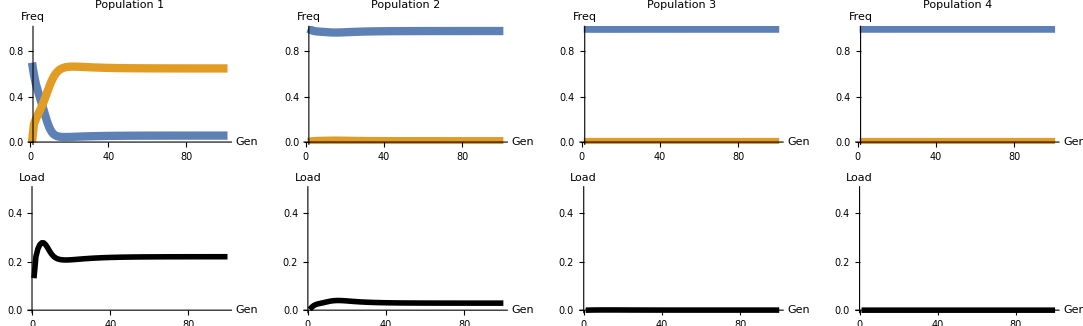

```mathematica
GraphicsGrid[{{P1,P2,P3,P4},{Load1,Load2,Load3,Load4}}]
```

# Graveyard code

```mathematica
(*Recombination[Fgenotypes_,pars_]:=
Block[{i,out=Table[0,{i,1,Length[#Genotypes &[pars]]}]},
For[i=1,i≤Length[Fgenotypes],++i,
Do[out[[Position[#Gametes  &[pars],k][[1,1]]]]+=
Fgenotypes[[i]] 1/2^Length[#Loci  &[pars]],{k,GameteRecombinants[Position[#Gametes &[pars],#Genotypes &[pars] [[i]][[1]]][[1,1]],Position[#Gametes &[pars] ,#Genotypes &[pars] [[i]][[2]]][[1,1]],pars]}];
];
out
]*)
```

```mathematica
(*Recombination[Fgametes_,pars_]:=Block[{i,j,out=ConstantArray[0,Length[Fgametes]]},
Assert[Total[Fgametes]==1];
For[i=1,i≤Length[Fgametes],++i,
For[j=1,j≤Length[Fgametes],++j,
Do[out[[Position[#Gametes  &[pars],k][[1,1]]]]+=
Fgametes[[i]]Fgametes[[j]] 1/2^Length[#Loci  &[pars]],{k,GameteRecombinants[i,j,pars]}];
];
];
out
]*)
```

```mathematica
(*Drive[Fgametes_,pars_]:=Block[{i,j,out=ConstantArray[0,Length[Fgametes]],Fgenotypes,FgenotypesPrime},
Assert[Total[Fgametes]==1];
Fgenotypes=ConvertToGenotypes[Fgametes,pars];
FgenotypesPrime= #DriveMatrix.Fgenotypes &[pars];
out = ConvertToGametes[FgenotypesPrime,pars];
out
]*)
```

```mathematica
(*Migration[Fgametes1_,Fgametes2_,pars_]:=Block[{},

]*)
```

```mathematica
(*DISCLAIMER: DUE TO TRACING OF GAMETE FREQUENCIES, NO INBREEDING COEFFICIENT KNOWN. CAREFUL WITH DRIVE*)
```

```mathematica
(*DiploidSelection[Fgametes_,pars_]:=
Block[{i,j,out=ConstantArray[0,Length[Fgametes]]},
Assert[Total[Fgametes]==1];
For[i=1,i≤Length[Fgametes],++i,
For[j=1,j≤Length[Fgametes],++j,
out[[i]]+=Fgametes[[i]] Fgametes[[j]] #Fitness[[Position[#Genotypes,{#Gametes[[i]],#Gametes[[j]]}][[1,1]]]] &[pars]
];
];
out/Total[out]
]*)
```